# Cuaderno de Prácticas

## Análisis y métodos numéricos

## Grado en Ingeniería Informática

## CURSO 2024/25

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : 2
Grupo de prácticas :

## Práctica 14

### Mínimos cuadrados

Encontrar la recta que mejor aproxime en el sentido de los mínimos cuadrados a los datos (1,1,), (2,3), (4,7), (7,12), (8,15).

```mathematica
p[x_]:= a+b*x
error[a_,b_]:=(p[1]-1)^2 +(p[2]-3)^2 +(p[4]-7)^2 +(p[7]-12)^2 +(p[8]-15)^2
error[a,b]
```

(-1+a+b)^2+(-3+a+2 b)^2+(-7+a+4 b)^2+(-12+a+7 b)^2+(-15+a+8 b)^2

```mathematica
Solve[{D[error[a,b],a]==0,D[error[a,b],b]==0},{a,b}]
```

{{a→-83/93,b→359/186}}

```mathematica
p[x]/.%
```

{-83/93+(359 x)/186}

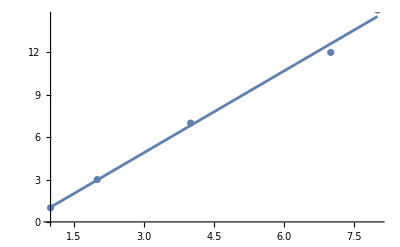

```mathematica
Show[Plot[-83/93+(359 x)/186,{x,1,8}],ListPlot[{{1,1},{2,3},{4,7},{7,12},{8,15}}]]
```

Calcular la parábola que mejor aproxima en el sentido de los mínimos cuadrados los datos (1,5),(2,4),(4,4),(7,12),(8,20),(10,30).

```mathematica
datos={{1,5},{2,4},{4,4},{7,12},{8,20},{10,30}};
n=Length[datos];
min=Min[Table[datos[[i]][[1]],{i,1,n}]];
max=Max[Table[datos[[i]][[1]],{i,1,n}]];
q[x_]:=a+b*x+c*x^2
er[a_,b_,c_]:=∑_(i=1)^n (q[datos[[i]][[1]]]-datos[[i]][[2]])^2 (* (q(xi)-yi)^2 *)
Solve[{D[er[a,b,c],a]==0,D[er[a,b,c],b]==0,D[er[a,b,c],c]==0},{a,b,c}]
```

{{a→12693/1810,b→-4719/1810,c→90/181}}

```mathematica
3. Calcular la función del tipo f(x) = a x^2+ bx+c que mejor aproxima en el sentido de los mínimos cuadrados los datos  (-2,2), (-1,1), (0,0), (1,-1),  (2,0) y (3,1).
	El sexto decimal de a es:
	A)  0,             B) 2,               C) 4,                      D) 6,            E) 8
	A)  8,             B) 0,               C) 2,                      D) 4,            E) 6
	El séptimo decimal de a es:
	A)  9,             B) 1,               C) 3,                      D) 5,            E) 7
	A)  1,             B) 3,               C) 5,                      D) 7,            E) 9 
	Aula de Informática. Julio 24
```

```mathematica
datos={{-2,2},{-1,1},{0,0},{1,-1},{2,0},{3,1}};
n=Length[datos];
p[x_]:=a*x^2+b*x+c
error[a_,b_,c_]:=Sum[(p[datos[[i,1]]]-datos[[i-2]])^2,{i,1,n}]
Solve[{D[error[a,b,c],a]==0,D[error[a,b,c],b]==0,D[error[a,b,c],c]==0},{a,b,c}]
```

{}

```mathematica
N[9/28,20]
```

0.32142857142857142857

### Ecuaciones no lineales

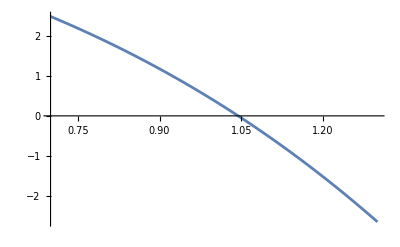

```mathematica
f[x_]:=x*Cos[x]-3 E^x+8
Plot[f[x],{x,0.7,1.3}]
```

```mathematica
a=0;
b=5;
If[f[a]*f[b]<0,
	Do[
		If[f[a]*f[(a+b)/2]>0,a=(a+b)/2,b=(a+b)/2]
	,30];
Print["La solución está entre ",N[a,20]," y ",N[b,20],
". Una aproximación sería ",N[(a+b)/2,20]," donde la función vale ",
 N[f[(a+b)/2],20]],
 Print["Cambia los puntos, no hay cambio de signo"]]
```

La solución está entre 1.0443607019260525703 y 1.0443607065826654434. Una aproximación sería 1.0443607042543590069 donde la función vale 1.7601280030052972459×10^-8

```mathematica
a=0;
b=5.;
If[f[a]*f[b]<0, Do[m=(b*f[a]-a*f[b])/(f[a]-f[b]);
	If[f[a]*f[m]>0,a=m,b=m],30];
Print["La solución está emtre ",N[a,20]," y ", N[b,20], ". Una aproximación sería ",
N[m,20]," donde la función vale ", N[f[m],20]],
Print["Cambia los puntos, no hay cambio de signo"]]
```

La solución está emtre 0.917376 y 5.. Una aproximación sería 0.917376 donde la función vale 1.04953